```mathematica
dateMouseSessionListV1={{"092120","Mouse21068","Session1"},{"092320","Mouse23336","Session1"},{"111520","Mouse23385","Session1"},{"111720","Mouse23385","Session1"},{"120520","Mouse23385","Session2"},{"121020","Mouse23312","Session4"},{"121320","Mouse23312","Session2"},{"010521","Mouse23332","Session1"},{"010721","Mouse23332","Session2"},{"011221","Mouse23332","Session4"},{"011921","Mouse23332","Session4"},{"011021","Mouse23305","Session2"},{"011221","Mouse23305","Session3"},{"020621","Mouse23305","Session4"},{"020721","Mouse23332","Session3"},{"020921","Mouse23305","Session4"},{"020921","Mouse23332","Session4"},{"030921","Mouse23324","Session4"},{"030721","Mouse23321","Session4"},{"031021","Mouse23321","Session4"},{"031721","Mouse23321","Session4"},{"072321","Mouse21135","Session1"},{"111321","Mouse22483","Session1"}};
```

```mathematica
dateMouseSessionListV2m={{"092420","Mouse21011","Session1"},{"092620","Mouse21069","Session2"},{"093020","Mouse21069","Session2"},{"100120","Mouse21069","Session2"},{"111420","Mouse23383","Session3"},{"111720","Mouse23383","Session1"},{"112220","Mouse23383","Session3"},{"111420","Mouse23386","Session3"},{"111720","Mouse23386","Session3"},{"120620","Mouse23383","Session2"},{"010221","Mouse23382","Session2"},{"010421","Mouse23382","Session2"},{"010621","Mouse23382","Session2"},{"011721","Mouse23390","Session2"},{"022821","Mouse23390","Session2"},{"030421","Mouse23390","Session1"},{"021321","Mouse23359","Session1"},{"022621","Mouse23310","Session2"},{"030221","Mouse23310","Session2"},{"031021","Mouse23310","Session2"},{"021821","Mouse23338","Session1"},{"031621","Mouse23338","Session1"},{"031821","Mouse23338","Session2"},{"081721","Mouse21151","Session1"},{"080221","Mouse22481","Session2"},{"072421","Mouse21133","Session2"},{"072121","Mouse21170","Session2"}};
```

```mathematica
(*********************************)
```

```mathematica
randDotCorrValsV1=Flatten[ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V1/ValuesForPlotting/motionCoherCorrVals_V1.txt","List"]];
```

```mathematica
randDotCorrValsV2m=Flatten[ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V2m/ValuesForPlotting/motionCoherCorrVals_V2m.txt","List"]];
```

```mathematica
(**********************)
```

```mathematica
v1Charts=Show[BoxWhiskerChart[randDotCorrValsV1,{{"Whiskers", Directive[Darker@Blue,Thick]}, {"Fences", Directive[Darker@Blue,Thick]},{"MedianMarker", Directive[Darker@Blue,Thickness[0.009]]}},PlotRange->{All,{-1,1}},ChartStyle->Directive[Blue,Opacity[0.3]],Frame->False],DistributionChart[randDotCorrValsV1,PlotRange->{All,{-1,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Blue],Frame->False],FrameTicks->{{LinTicks[-1,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
pmCharts=Show[BoxWhiskerChart[randDotCorrValsV2m,{{"Whiskers", Directive[Darker@Purple,Thick]}, {"Fences", Directive[Darker@Purple,Thick]},{"MedianMarker", Directive[Darker@Purple,Thickness[0.009]]}},PlotRange->{All,{-1,1}},ChartStyle->Directive[Purple,Opacity[0.3]],Frame->False],DistributionChart[randDotCorrValsV2m,PlotRange->{All,{-1,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Purple],Frame->False],FrameTicks->{{LinTicks[-1,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[BoxWhiskerChart[randDotCorrValsV2m,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},PlotRange->{All,{-1,1}},ChartStyle->Transparent,Frame->False],DistributionChart[randDotCorrValsV2m,PlotRange->{All,{-1,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False],FrameTicks->{{LinTicks[-1,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

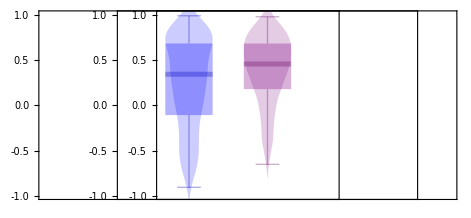

```mathematica
GraphicsRow[{v1Charts,pmCharts,transp},Spacings->{{-280,-280,-320}}]
```